```mathematica
(* global system *)
(* 
Note ex,ey,ez may vary depending on the person's orientation,
but are currently assumed to be aligned with gravitational vectors
(i.e. flat)
v0 (
*)

ClearAll["Global`*"]
MyTeXForm[a_]:=StringReplace[
StringReplace[ToString[TeXForm[a]],Shortest["\\text{"~~s___~~"}"]->s],
"$"->""]

ex={1,0,0};
ey={0,1,0};
ez={0,0,1};

(* System Parameters *)
ρ = 1000; (* kg/m^3 *)
fv [h_,R_,r_]:= (π h)/3(R^2+R r + r^2) (* frustum volume *)
(*m->ρ fv[4.33 2.54/100, 3.5 2.54/100, 2.32 2.54/100] *) (* derived mass *)

(* parameter values *)
(* lengths are currently arbitrary *)
params={
m-> 0.4, (* dunkin donuts medium size *)
lx->0.2,
ly->0.1,
lz->0.08,
g -> 9.81
};

(* person position / velocity *)
p0 = {0,0,0};
v0 = {0,0,0};

(* position / velocity *)

pa = p0 + lx ex + ly Cos[θx] ey + ly Sin[θx] ez;
pb = pa - ly Cos[θx] ey+ lz Sin[θy] ex - lz Cos[θy]ez;
va = v0 + Cross[ωx ex, pa-p0];
vb = Simplify[va + Cross[ωy (-Cos[θx]ey -Sin[θx]ez), pb-pa]];

(*Print["vb-va"]
MyTeXForm[Transpose[{Simplify[(vb-va)/ωy]}]]*)

p = pb;
v = vb;
(*
p = p0 + (lx + lz Sin[θy])ex + (ly Sin[θx] - lz Cos[θy]) ez;
v= v0 + ωx ly Cos[θx]ez - ωx ly Sin[θx]ey + ωy lz Sin[θy]ez + ωy lz Cos[θy]ex;
*)

(* energy *)
(* TODO : include KE of armature (device) *)
h = Dot[p, ez]
KE = Simplify[1/2 m  Dot[v,v]]
PE = Simplify[m g h]
```

-lz Cos[θy]+ly Sin[θx]

1/2 m (ωy^2 Cos[θx]^2 (lz Cos[θy]-ly Sin[θx])^2+Cos[θx]^2 (ly ωx+lz ωy Sin[θy])^2+Sin[θx]^2 (ly ωx+lz ωy Sin[θy])^2)

g m (-lz Cos[θy]+ly Sin[θx])

```mathematica
(* Lagrangian *)
L = KE-PE
L = L /. {θx -> θx[t], θy -> θy[t]};
L = L /. {ωx -> D[θx[t],t], ωy -> D[θy[t], t]};
Qx=D[(D[L, D[θx[t],t]]), t] - D[L, θx[t]]
Qy=D[(D[L, D[θy[t], t]]), t] - D[L, θy[t]]

sol = Solve[{Qx-τx[t] ==0,Qy - τy[t] ==0}, {θx''[t], θy''[t]}];
δx = Simplify[{θx''[t], θy''[t]}/.sol[[1]]] (* angular acc. *)
```

-g m (-lz Cos[θy]+ly Sin[θx])+1/2 m (ωy^2 Cos[θx]^2 (lz Cos[θy]-ly Sin[θx])^2+Cos[θx]^2 (ly ωx+lz ωy Sin[θy])^2+Sin[θx]^2 (ly ωx+lz ωy Sin[θy])^2)

g ly m Cos[θx[t]]-1/2 m (-2 ly Cos[θx[t]]^3 (lz Cos[θy[t]]-ly Sin[θx[t]]) θy'[t]^2-2 Cos[θx[t]] Sin[θx[t]] (lz Cos[θy[t]]-ly Sin[θx[t]])^2 θy'[t]^2)+1/2 m (2 ly Cos[θx[t]]^2 (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t])+2 ly Sin[θx[t]]^2 (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t]))

g lz m Sin[θy[t]]-1/2 m (-2 lz Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]]) Sin[θy[t]] θy'[t]^2+2 lz Cos[θx[t]]^2 Cos[θy[t]] θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t])+2 lz Cos[θy[t]] Sin[θx[t]]^2 θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t]))+1/2 m (-4 Cos[θx[t]] Sin[θx[t]] (lz Cos[θy[t]]-ly Sin[θx[t]])^2 θx'[t] θy'[t]+4 Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]]) θy'[t] (-ly Cos[θx[t]] θx'[t]-lz Sin[θy[t]] θy'[t])+2 lz Cos[θx[t]]^2 Cos[θy[t]] θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t])+2 lz Cos[θy[t]] Sin[θx[t]]^2 θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t])+2 Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2 θy''[t]+2 lz Cos[θx[t]]^2 Sin[θy[t]] (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t])+2 lz Sin[θx[t]]^2 Sin[θy[t]] (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t]))

{(Cos[θx[t]]^2 (Sec[θx[t]] (8 lz^2 Cos[θy[t]]^2 Sec[θx[t]]+(ly^2+4 lz^2-ly^2 Cos[4 θx[t]]-4 lz^2 Cos[2 θy[t]]) Sec[θx[t]]^3-16 ly lz Cos[θy[t]] Tan[θx[t]]) τx[t]-8 ly lz Sec[θx[t]]^4 Sin[θy[t]] τy[t]-m (2 g ly (4 lz^2 Cos[θy[t]]^2 Sec[θx[t]]+(3 ly^2-4 lz^2+6 ly^2 Cos[θx[t]]+4 ly^2 Cos[2 θx[t]]+2 ly^2 Cos[3 θx[t]]+ly^2 Cos[4 θx[t]]+4 lz^2 Cos[2 θy[t]]) Sec[θx[t]]^4 Sin[θx[t]/2]^2-8 ly lz Cos[θy[t]] Tan[θx[t]])+4 ly lz Sec[θx[t]]^3 Sin[θy[t]] (3 ly lz Cos[2 θx[t]-θy[t]]-2 ly lz Cos[θy[t]]+3 ly lz Cos[2 θx[t]+θy[t]]+2 ly^2 Sin[θx[t]]+2 lz^2 Sin[θx[t]]-2 ly^2 Sin[3 θx[t]]+lz^2 Sin[θx[t]-2 θy[t]]+lz^2 Sin[θx[t]+2 θy[t]]) θx'[t] θy'[t]-Sec[θx[t]] (-8 lz^4 Cos[θy[t]]^4 Sin[θx[t]]-8 ly lz^3 Cos[θx[t]/2]^2 Cos[θy[t]] Sec[θx[t]] ((7-10 Cos[θx[t]]+5 Cos[2 θx[t]]) Cos[θy[t]]^2+2 (3-2 Sec[θx[t]]) Sin[θy[t]]^2)+lz^2 Cos[θy[t]]^2 (3 ly^2-4 lz^2+16 ly^2 Cos[θx[t]]+12 ly^2 Cos[2 θx[t]]+9 ly^2 Cos[4 θx[t]]+4 lz^2 Cos[2 θy[t]]) Sec[θx[t]] Tan[θx[t]]-2 ly^3 lz (4+5 Cos[θx[t]]+7 Cos[3 θx[t]]) Cos[θy[t]] Sin[θx[t]] Tan[θx[t]]+8 ly^2 (ly^2 Cos[2 θx[t]] Sin[θx[t]]^3+lz^2 (1+Cos[2 θx[t]] Sec[θx[t]]) Sin[θy[t]]^2 Tan[θx[t]])) θy'[t]^2)))/(8 ly^2 m (lz Cos[θy[t]]-ly Sin[θx[t]])^2),(-lz Sec[θx[t]]^2 Sin[θy[t]] τx[t]+ly Sec[θx[t]]^2 τy[t]+m (ly (2 ly lz Cos[θx[t]] Cos[θy[t]]-ly^2 Sin[2 θx[t]]+2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2 Tan[θx[t]]) θx'[t] θy'[t]+lz (-g ly (-1+Sec[θx[t]]) Sec[θx[t]] Sin[θy[t]]+(ly lz Cos[θx[t]/2]^2 Sin[2 θy[t]]+lz^2 Cos[θy[t]]^2 Sin[θy[t]] Tan[θx[t]]+ly Sin[θx[t]] (-lz Sin[2 θy[t]] Tan[θx[t]]-ly Sin[θy[t]] (1+Cos[θx[t]]-Sin[θx[t]] Tan[θx[t]]))) θy'[t]^2)))/(ly m (lz Cos[θy[t]]-ly Sin[θx[t]])^2)}

```mathematica
state = {Ax[t], Ay[t], θx[t], θy[t], θx'[t], θy'[t]};
delta= {θx[t]-1, θy[t]-1, θx'[t], θy'[t], δx[[1]], δx[[2]]} (*against unit step*)
(*
state = {θx[t], θy[t], θx'[t], θy'[t]};
delta= {θx'[t], θy'[t], δx[[1]], δx[[2]]};
*)
input = {τx[t], τy[t]};
output = {θx[t], θy[t]}
sys = NonlinearStateSpaceModel[{delta,output}, state, input];
nsys = sys/.{Ax[t] -> Ax, Ay[t] -> Ay, θx'[t]-> ωx, θy'[t]->ωy, θx[t]->θx, θy[t]->θy, τx[t]->τx, τy[t]->τy}/.params
```

{-1+θx[t],-1+θy[t],θx'[t],θy'[t],(Cos[θx[t]]^2 (Sec[θx[t]] (8 lz^2 Cos[θy[t]]^2 Sec[θx[t]]+(ly^2+4 lz^2-ly^2 Cos[4 θx[t]]-4 lz^2 Cos[2 θy[t]]) Sec[θx[t]]^3-16 ly lz Cos[θy[t]] Tan[θx[t]]) τx[t]-8 ly lz Sec[θx[t]]^4 Sin[θy[t]] τy[t]-m (2 g ly (4 lz^2 Cos[θy[t]]^2 Sec[θx[t]]+(3 ly^2-4 lz^2+6 ly^2 Cos[θx[t]]+4 ly^2 Cos[2 θx[t]]+2 ly^2 Cos[3 θx[t]]+ly^2 Cos[4 θx[t]]+4 lz^2 Cos[2 θy[t]]) Sec[θx[t]]^4 Sin[θx[t]/2]^2-8 ly lz Cos[θy[t]] Tan[θx[t]])+4 ly lz Sec[θx[t]]^3 Sin[θy[t]] (3 ly lz Cos[2 θx[t]-θy[t]]-2 ly lz Cos[θy[t]]+3 ly lz Cos[2 θx[t]+θy[t]]+2 ly^2 Sin[θx[t]]+2 lz^2 Sin[θx[t]]-2 ly^2 Sin[3 θx[t]]+lz^2 Sin[θx[t]-2 θy[t]]+lz^2 Sin[θx[t]+2 θy[t]]) θx'[t] θy'[t]-Sec[θx[t]] (-8 lz^4 Cos[θy[t]]^4 Sin[θx[t]]-8 ly lz^3 Cos[θx[t]/2]^2 Cos[θy[t]] Sec[θx[t]] ((7-10 Cos[θx[t]]+5 Cos[2 θx[t]]) Cos[θy[t]]^2+2 (3-2 Sec[θx[t]]) Sin[θy[t]]^2)+lz^2 Cos[θy[t]]^2 (3 ly^2-4 lz^2+16 ly^2 Cos[θx[t]]+12 ly^2 Cos[2 θx[t]]+9 ly^2 Cos[4 θx[t]]+4 lz^2 Cos[2 θy[t]]) Sec[θx[t]] Tan[θx[t]]-2 ly^3 lz (4+5 Cos[θx[t]]+7 Cos[3 θx[t]]) Cos[θy[t]] Sin[θx[t]] Tan[θx[t]]+8 ly^2 (ly^2 Cos[2 θx[t]] Sin[θx[t]]^3+lz^2 (1+Cos[2 θx[t]] Sec[θx[t]]) Sin[θy[t]]^2 Tan[θx[t]])) θy'[t]^2)))/(8 ly^2 m (lz Cos[θy[t]]-ly Sin[θx[t]])^2),(-lz Sec[θx[t]]^2 Sin[θy[t]] τx[t]+ly Sec[θx[t]]^2 τy[t]+m (ly (2 ly lz Cos[θx[t]] Cos[θy[t]]-ly^2 Sin[2 θx[t]]+2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2 Tan[θx[t]]) θx'[t] θy'[t]+lz (-g ly (-1+Sec[θx[t]]) Sec[θx[t]] Sin[θy[t]]+(ly lz Cos[θx[t]/2]^2 Sin[2 θy[t]]+lz^2 Cos[θy[t]]^2 Sin[θy[t]] Tan[θx[t]]+ly Sin[θx[t]] (-lz Sin[2 θy[t]] Tan[θx[t]]-ly Sin[θy[t]] (1+Cos[θx[t]]-Sin[θx[t]] Tan[θx[t]]))) θy'[t]^2)))/(ly m (lz Cos[θy[t]]-ly Sin[θx[t]])^2)}

{θx[t],θy[t]}

-1+θx-1+θyωxωy(31.25 Cos[θx]^2 (-0.064 τy Sec[θx]^4 Sin[θy]+τx Sec[θx] (0.0512 Cos[θy]^2 Sec[θx]+(0.0356-0.01 Cos[4 θx]-0.0256 Cos[2 θy]) Sec[θx]^3-0.128 Cos[θy] Tan[θx])-0.4 (0.032 ωx ωy Sec[θx]^3 Sin[θy] (0.024 Cos[2 θx-θy]-0.016 Cos[θy]+0.024 Cos[2 θx+θy]+0.0328 Sin[θx]-0.02 Sin[3 θx]+0.0064 Sin[θx-2 θy]+0.0064 Sin[θx+2 θy])+1.962 (0.0256 Cos[θy]^2 Sec[θx]+(0.0044+0.06 Cos[θx]+0.04 Cos[2 θx]+0.02 Cos[3 θx]+0.01 Cos[4 θx]+0.0256 Cos[2 θy]) Sec[θx]^4 Sin[θx/2]^2-0.064 Cos[θy] Tan[θx])-ωy^2 Sec[θx] (-0.00032768 Cos[θy]^4 Sin[θx]-0.0004096 Cos[θx/2]^2 Cos[θy] Sec[θx] ((7-10 Cos[θx]+5 Cos[2 θx]) Cos[θy]^2+2 (3-2 Sec[θx]) Sin[θy]^2)+0.0064 Cos[θy]^2 (0.0044+0.16 Cos[θx]+0.12 Cos[2 θx]+0.09 Cos[4 θx]+0.0256 Cos[2 θy]) Sec[θx] Tan[θx]-0.00016 (4+5 Cos[θx]+7 Cos[3 θx]) Cos[θy] Sin[θx] Tan[θx]+0.08 (0.01 Cos[2 θx] Sin[θx]^3+0.0064 (1+Cos[2 θx] Sec[θx]) Sin[θy]^2 Tan[θx])))))/(0.08 Cos[θy]-0.1 Sin[θx])^2(25. (0.1 τy Sec[θx]^2-0.08 τx Sec[θx]^2 Sin[θy]+0.4 (0.1 ωx ωy (0.016 Cos[θx] Cos[θy]-0.01 Sin[2 θx]+2 (0.08 Cos[θy]-0.1 Sin[θx])^2 Tan[θx])+0.08 (-0.981 (-1+Sec[θx]) Sec[θx] Sin[θy]+ωy^2 (0.008 Cos[θx/2]^2 Sin[2 θy]+0.0064 Cos[θy]^2 Sin[θy] Tan[θx]+0.1 Sin[θx] (-0.08 Sin[2 θy] Tan[θx]-0.1 Sin[θy] (1+Cos[θx]-Sin[θx] Tan[θx])))))))/(0.08 Cos[θy]-0.1 Sin[θx])^2θxθyAxAyθxθyωxωy 6222NoneNoneFalseFalseFalse{τx,τy}Automatic

NDSolve::ndsz: At t == 0.0979495, step size is effectively zero; singularity or stiff system suspected.

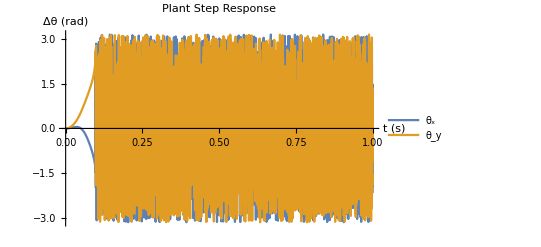

```mathematica
resp = OutputResponse[nsys, {1 * UnitStep[t],1 *UnitStep[t]}, {t,0,1.0}];
respx = resp[[1]];
respx = ArcTan[Cos[respx],Sin[respx]];
respy = resp[[2]];
respy = ArcTan[Cos[respy], Sin[respy]];
Plot[{respx, respy},{t,0,1},  PlotLegends->{"θ_x","θ_y"}, AxesLabel->{"t (s)","Δθ (rad)"}, PlotLabel->"Plant Step Response"]
```

```mathematica
(* Pole Placement *)
(*kpole = StateFeedbackGains[nsys,{-16+3I,-16-3I, -17+5I, -17-5I}]*)

(* LQR Controller *)
qcost = DiagonalMatrix[{1, 1, 1, 1, 1*^-1, 1*^-1}];
(*qcost = DiagonalMatrix[{ 1, 1, 1*^-1, 1*^-1}];*)

qycost = DiagonalMatrix[{1,1}];
rcost = DiagonalMatrix[{.1, .1}];
(*klqr = LQOutputRegulatorGains[nsys,{qycost, rcost}]*)(* τx, τy*)
klqr = LQRegulatorGains[nsys,{qcost, rcost}] (* τx, τy*)
kmat = TraditionalForm[Normal@CoefficientArrays[klqr,{Ax, Ay, θx,θy,ωx,ωy}][[2]]]
TraditionalForm[qcost]
TraditionalForm[rcost]
```

{0.+3.16228 Ax+4.05293 θx+1.01608 ωx,0.+3.16228 Ay+4.04843 θy+1.01031 ωy}

(3.16228 | 0 | 4.05293 | 0 | 1.01608 | 0
0 | 3.16228 | 0 | 4.04843 | 0 | 1.01031)

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1/10 | 0
0 | 0 | 0 | 0 | 0 | 1/10)

(0.1 | 0.
0. | 0.1)

{0.999948,0.999565}

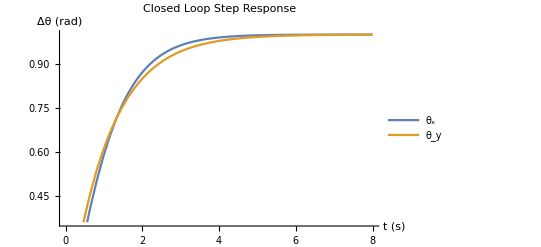

Part::partw: Part 2 of ref[0.000163429] does not exist.

Part::partw: Part 2 of ref[0.163429] does not exist.

Part::partw: Part 2 of ref[0.326694] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

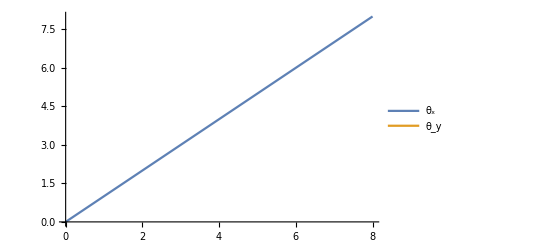

```mathematica
(* Closed-Loop Analysis *)
tlim = 8;
k =klqr;
nsyscl = SystemsModelStateFeedbackConnect[nsys, k];
ref[t] = 1*{UnitStep[t], UnitStep[t]};
rcl = OutputResponse[nsyscl, ref[t], {t,0,tlim}];
rcl/.{t->tlim} (* final value ... *)

Plot[rcl,{t,0,tlim},  PlotLegends->{"θ_x","θ_y"}, AxesLabel->{"t (s)","Δθ (rad)"}, PlotLabel->"Closed Loop Step Response"]
Plot[{ref[t][[1]], ref[t][[2]]},{t,0,tlim}, PlotLegends->{"θ_x","θ_y"}]
(*
ctrl = PIDTune[nsys, {"PID", Automatic}];
nsyscl = PIDTune[nsys, {"PID", Automatic}, "ReferenceOutput"];
(*nsysol = SystemsModelSeriesConnect[ctrl, nsys];
nsyscl = SystemsModelFeedbackConnect[nsysol, -1];
*)

respcl = OutputResponse[nsyscl, UnitStep[t], {t,0,10}];
Plot[%,{t,0,10}]*)
```

```mathematica
(* Jacobian ...*)
(*Jx = Simplify[D[δx, {{θx[t], θy[t]}}]]
Ju = Simplify[D[δx, {{τx[t], τy[t]}}]]

Simplify[Jx/.{θx[t]->0, θy[t]->0 , τx[t]-> 0, τy[t]->0 }]
Simplify[Ju/.{θx[t]->0, θy[t]->0 , τx[t]-> 0, τy[t]->0 }]*)

(* linearization *)
(*ldx = Series[δx, {θx[t], 0, 1}, {θy[t], 0, 1}] // Normal
LaplaceTransform[ldx,t,s]*)
```

```mathematica
(* Pretty *)

MyTeXForm[a_]:=StringReplace[
StringReplace[ToString[TeXForm[a]],Shortest["\\text{"~~s___~~"}"]->s],
{"$"->"", "\\left" -> "", "\\right" -> ""}]

unpretty = {
θx -> θx[t], θy -> θy[t],
ωx -> D[θx[t],t], ωy -> D[θy[t], t]
};
pretty = {
lx-> Subscript[l, x], ly-> Subscript[l, y], lz-> Subscript[l, z],
θx[t] -> Subscript[θ, x], D[θx[t],t] -> Subscript[ω, x], D[D[θx[t],t],t] -> Subscript[α, x],
θy[t] -> Subscript[θ, y], D[θy[t],t] -> Subscript[ω, y], D[D[θy[t],t],t] -> Subscript[α, y],
τx[t]-> Subscript[τ, x] ,τy[t] -> Subscript[τ, y] 
};

(*TraditionalForm[Simplify[Qx/.pretty]]
TraditionalForm[Simplify[Qy/.pretty]]
TraditionalForm[Simplify[δx/.pretty]]
TraditionalForm[Simplify[ldx/.pretty]]*)

ex = Simplify[δx[[1]]/.pretty];
MyTeXForm[ex]

ex = Simplify[δx[[2]]/.pretty];
MyTeXForm[ex]

(*MyTeXForm[Simplify[δx[[1]]/.pretty]]
MyTeXForm[Simplify[δx[[2]]/.pretty]]*)

(* ... *)
Qx/.params;
Qy/.params;
```

\frac{8 l_y l_z (l_z (2 g m \sin ^2(\frac{\theta _x}{2}) \sec ^2(\theta _x) \sin ^2(\theta _y)-g m \cos (\theta _x) \cos ^2(\theta _y))+m l_z^2 \omega _y \cos (\theta _y) (\omega _y \cos ^2(\frac{\theta _x}{2}) ((10 \cos (\theta _x)-5 \cos (2 \theta _x)-7) \cos ^2(\theta _y)+2 (2 \sec (\theta _x)-3) \sin ^2(\theta _y))-\omega _x \tan (\theta _x) \sin (2 \theta _y))-2 \tau _x \sin (\theta _x) \cos (\theta _y)+\tau _y \sec ^2(\theta _x) (-\sin (\theta _y)))+l_y^2 (8 g m l_z \sin (2 \theta _x) \cos (\theta _y)+m l_z^2 \omega _y (\omega _y ((16 \sin (\theta _x)-6 \sin (2 \theta _x)+9 \sin (4 \theta _x)) \cos ^2(\theta _y)+8 \sin ^2(\theta _y) (\sin (\theta _x)+\cos (2 \theta _x) \tan (\theta _x)))-4 \omega _x (3 \cos (2 \theta _x)-1) \sec (\theta _x) \sin (2 \theta _y))+8 \tau _x \sin ^2(\theta _x))-2 m l_y^3 (4 g \sin ^2(\theta _x) \cos (\theta _x)+l_z \omega _y (\omega _y \sin ^2(\theta _x) (5 \cos (\theta _x)+7 \cos (3 \theta _x)+4) \cos (\theta _y)-8 \omega _x \cos (2 \theta _x) \tan (\theta _x) \sin (\theta _y)))+2 m l_y^4 \omega _y^2 \sin ^2(\theta _x) \sin (4 \theta _x)-4 l_z^2 (m l_z^2 \omega _y^2 \cos ^2(\theta _y) (2 \tan (\theta _x) \sin ^2(\theta _y)+\sin (2 \theta _x) \cos ^2(\theta _y))-2 \tau _x (\sec ^2(\theta _x) \sin ^2(\theta _y)+\cos ^2(\theta _y)))}{8 m l_y^2 (l_y \sin (\theta _x)-l_z \cos (\theta _y)){}^2}

\frac{m (l_z (\omega _y^2 (l_y l_z \cos ^2(\frac{\theta _x}{2}) \sin (2 \theta _y)+l_z^2 \tan (\theta _x) \sin (\theta _y) \cos ^2(\theta _y)+l_y \sin (\theta _x) (l_z \tan (\theta _x) (-\sin (2 \theta _y))-l_y \sin (\theta _y) (\cos (\theta _x)-\sin (\theta _x) \tan (\theta _x)+1)))-g l_y (\sec (\theta _x)-1) \sec (\theta _x) \sin (\theta _y))+l_y \omega _x \omega _y (l_y^2 (-\sin (2 \theta _x))+2 l_y l_z \cos (\theta _x) \cos (\theta _y)+2 \tan (\theta _x) (l_y \sin (\theta _x)-l_z \cos (\theta _y)){}^2))+l_y \tau _y \sec ^2(\theta _x)+l_z \tau _x \sec ^2(\theta _x) (-\sin (\theta _y))}{m l_y (l_y \sin (\theta _x)-l_z \cos (\theta _y)){}^2}

```mathematica
TraditionalForm[Simplify[δx[[1]]/.pretty]]
```

1/(8 m l_y^2 (l_y sin(θ_x)-l_z cos(θ_y))^2)(8 l_y l_z (l_z (2 g m sin^2(θ_x/2) sec^2(θ_x) sin^2(θ_y)-g m cos(θ_x) cos^2(θ_y))+m l_z^2 ω_y cos(θ_y) (ω_y cos^2(θ_x/2) ((10 cos(θ_x)-5 cos(2 θ_x)-7) cos^2(θ_y)+2 (2 sec(θ_x)-3) sin^2(θ_y))-ω_x tan(θ_x) sin(2 θ_y))-2 τ_x sin(θ_x) cos(θ_y)+τ_y sec^2(θ_x) (-sin(θ_y)))+l_y^2 (8 g m l_z sin(2 θ_x) cos(θ_y)+m l_z^2 ω_y (ω_y ((16 sin(θ_x)-6 sin(2 θ_x)+9 sin(4 θ_x)) cos^2(θ_y)+8 sin^2(θ_y) (sin(θ_x)+cos(2 θ_x) tan(θ_x)))-4 ω_x (3 cos(2 θ_x)-1) sec(θ_x) sin(2 θ_y))+8 τ_x sin^2(θ_x))-2 m l_y^3 (4 g sin^2(θ_x) cos(θ_x)+l_z ω_y (ω_y sin^2(θ_x) (5 cos(θ_x)+7 cos(3 θ_x)+4) cos(θ_y)-8 ω_x cos(2 θ_x) tan(θ_x) sin(θ_y)))+2 m l_y^4 ω_y^2 sin^2(θ_x) sin(4 θ_x)-4 l_z^2 (m l_z^2 ω_y^2 cos^2(θ_y) (2 tan(θ_x) sin^2(θ_y)+sin(2 θ_x) cos^2(θ_y))-2 τ_x (sec^2(θ_x) sin^2(θ_y)+cos^2(θ_y))))

```mathematica
<<ToMatlab`
```

```mathematica
mpretty = {
lx-> lx, ly-> ly, lz-> lz,
θx[t] -> tx, D[θx[t],t] -> wx, D[D[θx[t],t],t] -> ax,
θy[t] -> ty, D[θy[t],t] -> wy, D[D[θy[t],t],t] -> ay,
τx[t]-> ux ,τy[t] -> uy 
};
ToMatlab[δx/.mpretty]
```

[(1/8).*ly.^(-2).*m.^(-1).*cos(tx).^2.*(lz.*cos(ty)+(-1).*ly.*sin( ...
  tx)).^(-2).*((-8).*ly.*lz.*uy.*sec(tx).^4.*sin(ty)+ux.*sec(tx).*( ...
  8.*lz.^2.*cos(ty).^2.*sec(tx)+(ly.^2+4.*lz.^2+(-1).*ly.^2.*cos(4.* ...
  tx)+(-4).*lz.^2.*cos(2.*ty)).*sec(tx).^3+(-16).*ly.*lz.*cos(ty).* ...
  tan(tx))+(-1).*m.*(4.*ly.*lz.*wx.*wy.*sec(tx).^3.*sin(ty).*(3.* ...
  ly.*lz.*cos(2.*tx+(-1).*ty)+(-2).*ly.*lz.*cos(ty)+3.*ly.*lz.*cos( ...
  2.*tx+ty)+2.*ly.^2.*sin(tx)+2.*lz.^2.*sin(tx)+(-2).*ly.^2.*sin(3.* ...
  tx)+lz.^2.*sin(tx+(-2).*ty)+lz.^2.*sin(tx+2.*ty))+2.*g.*ly.*(4.* ...
  lz.^2.*cos(ty).^2.*sec(tx)+(3.*ly.^2+(-4).*lz.^2+6.*ly.^2.*cos(tx) ...
  +4.*ly.^2.*cos(2.*tx)+2.*ly.^2.*cos(3.*tx)+ly.^2.*cos(4.*tx)+4.* ...
  lz.^2.*cos(2.*ty)).*sec(tx).^4.*sin((1/2).*tx).^2+(-8).*ly.*lz.* ...
  cos(ty).*tan(tx))+(-1).*wy.^2.*sec(tx).*((-8).*lz.^4.*cos(ty).^4.* ...
  sin(tx)+(-8).*ly.*lz.^3.*cos((1/2).*tx).^2.*cos(ty).*sec(tx).*((7+ ...
  (-10).*cos(tx)+5.*cos(2.*tx)).*cos(ty).^2+2.*(3+(-2).*sec(tx)).* ...
  sin(ty).^2)+lz.^2.*cos(ty).^2.*(3.*ly.^2+(-4).*lz.^2+16.*ly.^2.* ...
  cos(tx)+12.*ly.^2.*cos(2.*tx)+9.*ly.^2.*cos(4.*tx)+4.*lz.^2.*cos( ...
  2.*ty)).*sec(tx).*tan(tx)+(-2).*ly.^3.*lz.*(4+5.*cos(tx)+7.*cos( ...
  3.*tx)).*cos(ty).*sin(tx).*tan(tx)+8.*ly.^2.*(ly.^2.*cos(2.*tx).* ...
  sin(tx).^3+lz.^2.*(1+cos(2.*tx).*sec(tx)).*sin(ty).^2.*tan(tx))))) ...
  ,ly.^(-1).*m.^(-1).*(lz.*cos(ty)+(-1).*ly.*sin(tx)).^(-2).*(ly.* ...
  uy.*sec(tx).^2+(-1).*lz.*ux.*sec(tx).^2.*sin(ty)+m.*(ly.*wx.*wy.*( ...
  2.*ly.*lz.*cos(tx).*cos(ty)+(-1).*ly.^2.*sin(2.*tx)+2.*(lz.*cos( ...
  ty)+(-1).*ly.*sin(tx)).^2.*tan(tx))+lz.*((-1).*g.*ly.*((-1)+sec( ...
  tx)).*sec(tx).*sin(ty)+wy.^2.*(ly.*lz.*cos((1/2).*tx).^2.*sin(2.* ...
  ty)+lz.^2.*cos(ty).^2.*sin(ty).*tan(tx)+ly.*sin(tx).*((-1).*lz.* ...
  sin(2.*ty).*tan(tx)+(-1).*ly.*sin(ty).*(1+cos(tx)+(-1).*sin(tx).* ...
  tan(tx)))))))];

```mathematica
p
```

{lx+lz Sin[θy],0,-lz Cos[θy]+ly Sin[θx]}